# Long form data transformation

## Introduction

In this notebook we consider in more detail the (tabular) data transformation operations Long form.

Remark: This notebook is an expanded version of the notebook used in the Wolfram U session [AAv2].

Remark: We use several Wolfram Function Repository (WFR) functions: ExampleDataset and RandomTabularDataset.

Load the paclet

```mathematica
Needs["AntonAntonov`DataReshapers`"]
```

## What kind of data?

We concentrate on using data frames (datasets).

More precisely tabular data and simple collections of tabular data.

I.e. in WL -- datasets or lists or associations of datasets.

## What workflows considered?

Here is a flow chart that shows the targeted workflows:

```mathematica
plWorkflows=ImageCrop@Import["https://github.com/antononcube/ConversationalAgents/raw/master/ConceptualDiagrams/Tabular-data-transformation-workflows.jpg"]
```

-Graphics-

## Long form in more detail

Remark: This “Illustrating example 2” from the tech note "Data transformation workflows". (Also, session [AAv1].)

#### Column names as data

Take a dataset with time series specified through separate columns and convert into easier to query dataset:

Get the Lake Mead levels data

```mathematica
ExampleData[{"Statistics","LakeMeadLevels"},"LongDescription"]
```

Elevation of Lake Mead at Hoover Dam, in feet, in years 1935-2009.  The observation on January of 1935 was missing.

Get the Lake Mead levels dataset

```mathematica
dsLakeData=ResourceFunction["ExampleDataset"][{"Statistics","LakeMeadLevels"}]
```

Convert to long form

```mathematica
dsLong=LongFormDataset[dsLakeData,"Year","VariablesTo"->"Month","ValuesTo"->"Elevation"]
```

Modify month from string value to integer value

```mathematica
dsLong=dsLong[All,Join[#,<|"Month"->DateList[{#Month,{"MonthShort"}}]⟦2⟧|>]&]
```

Group by year and show short form of the result

```mathematica
GroupBy[Normal@dsLong,#Year&]//Short
```

<|1935→{<|Year→1935,Month→4,Elevation→752.4|>,«10»,<|Year→1935,Month→9,Elevation→920.8|>},«73»,2009→{«1»}|>

For each year find the corresponding time series (of lake levels)

```mathematica
timeSeriesCollection=GroupBy[Normal@dsLong,#Year&,TimeSeries[Values/@#⟦All,{"Month","Elevation"}⟧]&];
Length[timeSeriesCollection]
```

75

Show a sample of the time series found above

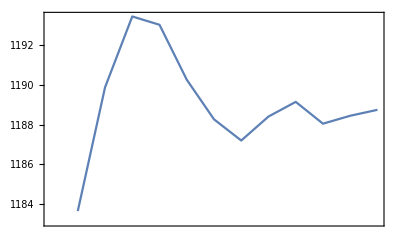
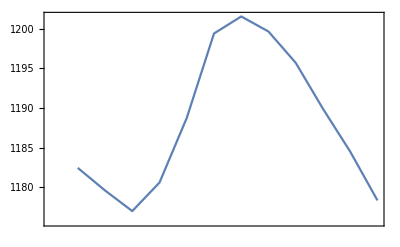
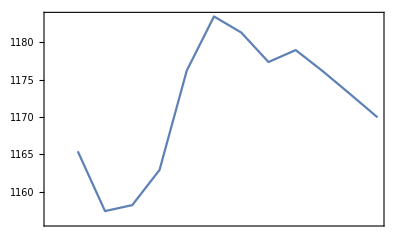
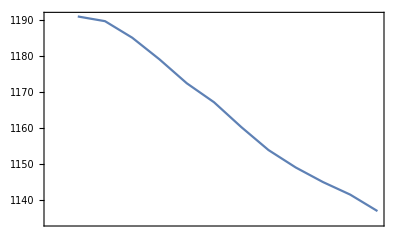
<|1993→-Graphics-,1943→-Graphics-,1939→-Graphics-,1963→-Graphics-|>

```mathematica
SeedRandom[23];
DateListPlot/@RandomSample[timeSeriesCollection,4]
```

### Calendar time series

The previous time series are relative in time. What if we want to do calendar time series?

First we have to modify the month column to be "ObservationTime":

```mathematica
dsLong2=dsLong[All,Join[#,<|"ObservationTime"->AbsoluteTime[ToString[#Year]<>"-"<>ToString[#Month]]|>]&]
```

Split the long form dataset by year and make time series with the columns "ObservationTime" and "Elevation":

```mathematica
timeSeriesCollection2=GroupBy[Normal@dsLong2,#Year&,TimeSeries[Values/@#⟦All,{"ObservationTime","Elevation"}⟧]&];
Length[timeSeriesCollection2]
```

75

Plot the obtained time series:

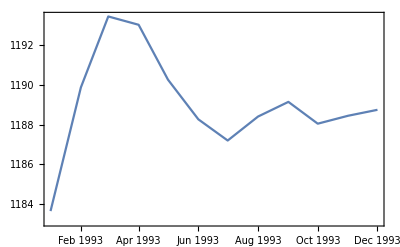
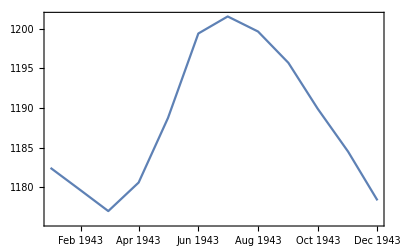
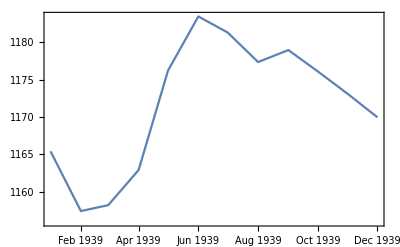
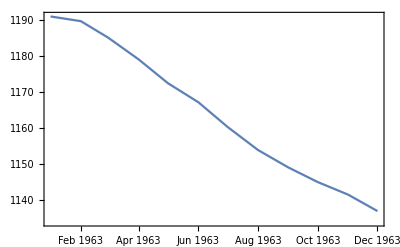
<|1993→-Graphics-,1943→-Graphics-,1939→-Graphics-,1963→-Graphics-|>

```mathematica
SeedRandom[23];
DateListPlot/@RandomSample[timeSeriesCollection2,4]
```

### Alternative solution without long form

(This sub-section was not discussed in Wolfram U recording of the “Q&A Introduction” session. It is given in this notebook in order to make a more convenient reference.)

We can apply the Split-Transform-Combine pattern directly without using long form:

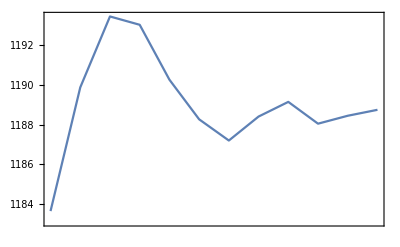
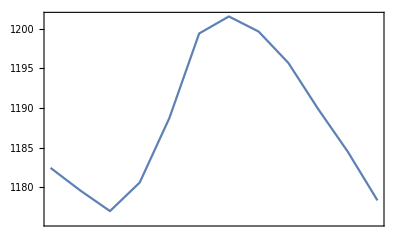
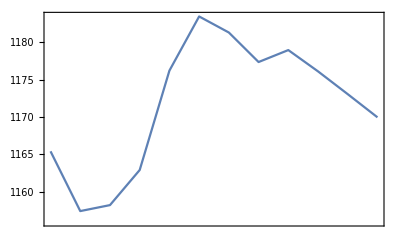
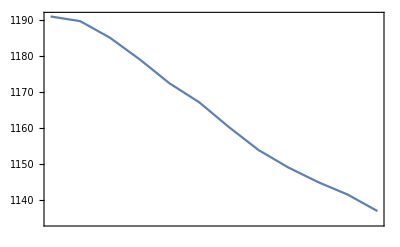
<|1993→-Graphics-,1943→-Graphics-,1939→-Graphics-,1963→-Graphics-|>

```mathematica
SeedRandom[23];
GroupBy[Normal@dsLakeData,#Year&,TimeSeries@Rest@Values@First@#&]//(DateListPlot/@RandomSample[#,4]&)
```

Note that:

In the transformation above we implicitly rely on the sorted order of the month name columns.

Using Rest and First in the third argument given to GroupBy corresponds to the transformations to get the long form.

## Long form applications

Many applications of Long form transformation come from the fact that metadata is converted to data

#### Combinations of the heterogenous data

Using long forms makes easier the programmatic manipulation of heterogenous data.

Get datasets with different number of rows and columns that correspond to items and variables of different kinds:

```mathematica
datasets=Association@Map[#->ResourceFunction["ExampleDataset"][{"Statistics",#}]&,{"AnimalWeights","EmployeeAttitude","OrangeTreeGrowth"}];
Magnify[#,1]&/@datasets
```

<|AnimalWeights→,EmployeeAttitude→,OrangeTreeGrowth→|>

Convert all datasets into long form datasets:

```mathematica
datasets=LongFormDataset/@datasets;
Magnify[#,0.8]&/@datasets
```

<|AnimalWeights→,EmployeeAttitude→,OrangeTreeGrowth→|>

For each long form dataset change the automatic key column to include dataset's name:

```mathematica
datasets=KeyValueMap[Function[{k,v},v[All,Prepend[#,"AutomaticKey"->k<>"-"<>ToString[#AutomaticKey]]&]],datasets];
Magnify[#,0.8]&/@datasets
```

{,,}

Join all long form datasets into one dataset and show a sample:

```mathematica
Dimensions[Join@@datasets]
```

{399,3}

```mathematica
SeedRandom[321];
Sort@RandomSample[Join@@datasets,8]
```

## Long form vs sparse array

Sparse matrices (sparse arrays) have representation very similar to that of long form. Here is a random sparse matrix:

Generate random (sparse) matrix

```mathematica
SeedRandom[12];
smat=SparseArray[RandomReal[{0,1},{4,5}]/.(x_?NumberQ/;x<0.5)->0]
```

SparseArray[…]

Matrix form of the random matrix

```mathematica
MatrixForm[smat]
```

(0 | 0 | 0.521411 | 0 | 0
0 | 0.749505 | 0 | 0.824845 | 0.89881
0.668975 | 0 | 0.734391 | 0 | 0.528677
0 | 0 | 0 | 0.836637 | 0)

Matrix plot of the random matrix

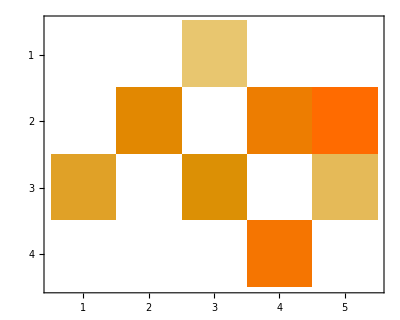

```mathematica
MatrixPlot[smat]
```

Compare the array rules of that sparse matrix with its long form representation.

Here are the array rules:

```mathematica
ArrayRules[smat]
```

{{1,3}→0.521411,{2,2}→0.749505,{2,4}→0.824845,{2,5}→0.89881,{3,1}→0.668975,{3,3}→0.734391,{3,5}→0.528677,{4,4}→0.836637,{_,_}→0}

Here is tabulation of the array rules:

```mathematica
ColumnForm@Map[Flatten,List@@@Most[ArrayRules[smat]]]
```

{1,3,0.521411}
{2,2,0.749505}
{2,4,0.824845}
{2,5,0.89881}
{3,1,0.668975}
{3,3,0.734391}
{3,5,0.528677}
{4,4,0.836637}

Here is the long form representation:

```mathematica
dsLong3=LongFormDataset[Normal@smat][Select[#Value>0&]]
```

Sort the long form dataset:

```mathematica
ReverseSortBy[dsLong3,{#Variable,#Value}&]
```

Note that since using Normal on the sparse matrix makes a dense matrix with zeroes, those zeroes are filtered out from the displayed long form.

Cross tabulate the long form

```mathematica
CrossTabulate[dsLong3]
```

Matrix form of the corresponding sparse matrix:

```mathematica
MatrixForm[smat]
```

(0 | 0 | 0.521411 | 0 | 0
0 | 0.749505 | 0 | 0.824845 | 0.89881
0.668975 | 0 | 0.734391 | 0 | 0.528677
0 | 0 | 0 | 0.836637 | 0)

Here is comparison of the representations of sparse arrays vs long form:

```mathematica
GridTableForm[{{"Sparse array rules","Matrix representation"},{"Long form","Cross tabulation"}},TableHeadings->{"Data structure (long form)","Representation (wide form)"}]
```

# | Data structure (long form) | Representation (wide form)
1 | Sparse array rules | Matrix representation
2 | Long form | Cross tabulation

## References

Wide and narrow data - Wikipedia

[AA1] Anton Antonov, Contingency tables creation examples | Mathematica for prediction algorithms

[AAv1] Anton Antonov, "Data Transformation Workflows with Anton Antonov, Session #1", (2020), Wolfram channel at YouTube.

[AAv2] Anton Antonov, "Data Transformation Workflows with Anton Antonov, Session #2", (2020), Wolfram channel at YouTube.

[AAv3] Anton Antonov, "Multi-language Data-Wrangling Conversational Agent", (2021), Wolfram Technology Conference 2020 presentation, Wolfram channel at YouTube.

Related Guides

Data reshaping functions

Related Tech Notes

Data transformation workflows

Wide form data transformation

## Metadata

### Categorization

Tech Note

AntonAntonov/DataReshapers

AntonAntonov`DataReshapers`

AntonAntonov/DataReshapers/tutorial/Longformdatatransformation

### Keywords

Cross tabulation

Contingency matrix

Contingency table

Data transformation

Long form

Wide form